```mathematica
path="~/WORK/probe_particle_code/TOAT_aims/single_mol/symmetric_lda/";
inp=Import[path<>"/KS_eigenvectors.out","Table"];
eigen=Drop[Import[path<>"/all_states.dat","Table",HeaderLines->1],-2];
maxOrb=Max[eigen[[All,1]]]
geom=Import[path<>"/geometry.in","Table"][[All,5]];
```

172

```mathematica
numBasis=1110;(*|Total number of basis functions:*)
```

```mathematica
header=inp[[Range[2,numBasis+1],Range[2,6]]];
coefsi[i_]:=Quotient[i-1,5]*(numBasis+2)+Range[2,numBasis+1]
coefsj[i_]:=7+Mod[i-1,5]
```

```mathematica
For[j=1,j≤Length[eigen],j++,If[eigen[[j,4]]>-10,{n1=j,Print[j],Break[]}]]
For[j=n1,j≤Length[eigen],j++,If[eigen[[j,4]]>5,{n2=j,Print[j],Break[]},n2=numBasis]]
n2-n1+1
```

67

133

67

```mathematica
lcaocoefs=Array[Null,{n2-n1+1}];
For[j=n1,j≤n2,j++,{lcaocoefs[[j-n1+1]]=inp[[coefsi[j],coefsj[j]]]}]
```

```mathematica
species={"H","C","N","O"(*,"Cu"*)};
```

```mathematica
lmax={1,2,2,1,3,4,4};
o[1]:="_s.dat"
o[2]:="_p.dat"
o[3]:="_d.dat"
For[i=1,i≤Length[species],i++,{n[i_]:=ElementData[species[[i]],"Period"]}]
name[i_,k_,l_]:=path<>"/at_"<>ToString[i]<>"_"<>ToString[k]<>"_"<>ToString[n[i]]<>o[l];

For[i=1,i≤Length[species],i++,{For[l=1,l≤lmax[[n[i]]],l++,{For[k=1,k≤100,k++,If[FileExistsQ[name[i,k,l]],{Print[name[i,k,l]],R[i,l]=Import[name[i,k,l],"Table",HeaderLines->1]}]]}]}]
```

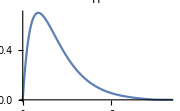
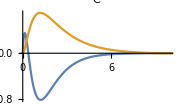
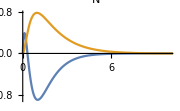
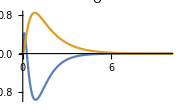

```mathematica
Table[{ListLinePlot[Table[R[i,l],{l,1,lmax[[n[i]]]}],PlotRange->{{0,10},All},PlotLabel->species[[i]],LabelStyle->Directive[Black,8],ImageSize->Small,PlotLegends->{"s","p","d}"}]},{i,1,Length[species]}]//TableForm
```

```mathematica
point=6;
For[i=1,i≤Length[species],i++,For[l=1,l≤lmax[[n[i]]],l++,For[k=1,k≤Length[R[i,l]],k++,{tmp=R[i,l];If[tmp[[k,1]]≤6,sign[i,l]=Sign[tmp[[k,2]]]]}]]];
tmp=.;Table[Table[sign[i,l],{l,1,lmax[[n[i]]]}],{i,1,Length[species]}]//TableForm
```

1 | 
-1 | 1
-1 | 1
-1 | 1

```mathematica
atspec=geom;For[i=1,i<=Length[geom],i++,For[j=1,j≤Length[species],j++,If[species[[j]]==ToString[geom[[i]]],atspec[[i]]=j]]];
atspec[[Range[1,10]]]//TableForm
```

3
2
2
2
2
2
2
2
2
2

```mathematica
(*pos[jj,atom]*)
ai=1;
For[i=1,i≤numBasis,i++,If[ai>Length[geom],Break[],{If[header[[i,{1,2,3}]]=={ai,"atomic",n[atspec[[ai]]]},If[header[[i,4]]=="s",{pos[1,ai]=i,If[lmax[[n[atspec[[ai]]]]]==1,ai=ai+1]},If[lmax[[n[atspec[[ai]]]]]>1,{If[header[[i,{4,5}]]=={"p",-1},pos[2,ai]=i,If[header[[i,{4,5}]]=={"p",0},pos[3,ai]=i,If[header[[i,{4,5}]]=={"p",1},{pos[4,ai]=i,ai=ai+1}]]]},ai=ai+1]]]}]]
Print[ai-1]
Print[Length[geom]]
```

34

34

```mathematica
jjmax=4;(*sp*)
eig=eigen[[Range[n1,n2],4]];
TranCoefs=Array[Null,{jjmax,(n2-n1+1),Length[geom]*2+1}];
TranCoefs[[All,All,All]]=0.0;
For[i=1,i≤jjmax,i++,{TranCoefs[[i,All,1]]=eig[[All]]}];
eig=.;
TranCoefs[[1,All,1]]//TableForm
```

```mathematica
signJ={1,1,1,-1};(*Dont change, means - +s, +py +pz -px*)
For[jj=1,jj≤jjmax,jj++,{If[jj==1,l=1,If[jj≤4,l=2,{Print[problem],Break}]],For[ii=1,ii≤n2-n1+1,ii++,For[i=1,i≤Length[geom],i++,If[jj≤(lmax[[n[atspec[[i]]]]]^2),(*Print[jj," ",i," ",pos[jj,i]]*)TranCoefs[[jj,ii,2*i]]=lcaocoefs[[ii,pos[jj,i]]]*sign[atspec[[i]],l] *signJ[[jj]] (*,Print[i]*) ]]]}];
```

```mathematica
TableForm[TranCoefs[[1,Range[100,120],All]](*,TableDirections->Row*)]
```

-7.17499 | 0. | 0. | -0.000601 | 0. | -0.00066 | 0. | 0.00005 | 0. | 0.000554 | 0. | 0.000559 | 0. | -0.00093 | 0. | 0.000535 | 0. | -0.000126 | 0. | -0.00029 | 0. | -0.000441 | 0. | 0.000304 | 0. | 0.0004 | 0. | 0.000913 | 0. | -0.000597 | 0. | 0.000096 | 0. | -0.000255 | 0. | 0.000194 | 0. | 0.000035 | 0. | -0.000175 | 0. | 0.000376 | 0. | 0.000046 | 0. | -0.000121 | 0. | -0.000512 | 0. | -0.000691 | 0. | 0.000543 | 0. | 0.000653 | 0. | 0.000049 | 0. | 0.000469 | 0. | 0.000057 | 0. | -0.000423 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.006581 | 0. | 0.019572 | 0. | -0.039881 | 0. | -0.004969 | 0. | 0.017334 | 0. | 0.007726 | 0. | -0.018226 | 0. | 0.00726 | 0. | -0.000828 | 0. | 0.026763 | 0. | -0.000917 | 0. | 0.006547 | 0. | -0.01416 | 0. | -0.002971 | 0. | -0.009811 | 0. | 0.00985 | 0. | 0.010182 | 0. | 0.006206 | 0. | -0.011774 | 0. | -0.005799 | 0. | -0.024127 | 0. | -0.007625 | 0. | -0.003803 | 0. | 0.014996 | 0. | 0.012266 | 0. | -0.018648 | 0. | 0.006348 | 0. | 0.009898 | 0. | 0.038916 | 0. | -0.001449 | 0. | -0.027384 | 0. | -0.023842 | 0. | -0.006752 | 0. | 0.016271 | 0. | -0.007099 | 0. | -0.002169 | 0. | 0.008266 | 0. | 0.006915 | 0. | -0.008885 | 0. | -0.008851 | 0. | 0.037032 | 0. | -0.011309 | 0. | 0.001044 | 0. | 0.000019 | 0. | -0.010904 | 0. | 0.019286 | 0. | 0.011815 | 0. | -0.007138 | 0. | 0.008483 | 0. | -0.006275 | 0. | 0.039121 | 0. | 0.002034 | 0. | 0.001644 | 0. | -0.026573 | 0. | -0.003127 | 0. | -0.012214 | 0. | -0.007981 | 0. | -0.000057 | 0. | 0.007642 | 0. | -0.019965 | 0. | -0.041992 | 0. | 0.015309 | 0. | -0.017832 | 0. | 0.022922 | 0. | 0.00095 | 0. | -0.001172 | 0. | 0.010211 | 0. | -0.016309 | 0. | -0.012211 | 0. | -0.001029 | 0. | -0.017045 | 0. | 0.00495 | 0. | 0.023682 | 0. | 0.021334 | 0. | -0.003357 | 0. | 0.012633 | 0. | 0.022408 | 0. | 0.017493 | 0. | 0.024598 | 0. | -0.010895 | 0. | 0.000627 | 0. | -0.034191 | 0. | -0.022435 | 0. | 0.012531 | 0. | 0.018826 | 0. | -0.015467 | 0. | -0.036266 | 0. | 0.003633 | 0. | -0.02907 | 0. | 0.041516 | 0. | 0.014331 | 0.
-7.16625 | -0.000654 | 0. | 0.000326 | 0. | -0.000271 | 0. | -0.00012 | 0. | -0.000268 | 0. | 0.00032 | 0. | -0.000273 | 0. | -0.000118 | 0. | -0.00005 | 0. | -0.000055 | 0. | 0.001068 | 0. | -0.000043 | 0. | 0.001073 | 0. | -0.000266 | 0. | -0.000124 | 0. | -0.000046 | 0. | -0.000267 | 0. | -0.000046 | 0. | 0.00107 | 0. | -0.000041 | 0. | -0.000268 | 0. | 0.00032 | 0. | 0.000321 | 0. | 0.000316 | 0. | 0.000787 | 0. | 0.000326 | 0. | 0.000779 | 0. | 0.000316 | 0. | 0.000321 | 0. | 0.000776 | 0. | 0.000324 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.001086 | 0. | 0.01252 | 0. | -0.011774 | 0. | 0.008297 | 0. | -0.00024 | 0. | -0.008929 | 0. | -0.005217 | 0. | 0.00463 | 0. | 0.008418 | 0. | -0.008831 | 0. | 0.00819 | 0. | -0.007872 | 0. | 0.012564 | 0. | -0.000548 | 0. | -0.011725 | 0. | 0.001034 | 0. | 0.014521 | 0. | -0.005115 | 0. | -0.013945 | 0. | 0.004741 | 0. | 0.001024 | 0. | 0.000351 | 0. | 0.01452 | 0. | -0.000351 | 0. | -0.013931 | 0. | -0.00037 | 0. | -0.000622 | 0. | 0.015076 | 0. | -0.011795 | 0. | -0.014952 | 0. | 0.012475 | 0. | -0.000605 | 0. | 0.004657 | 0. | -0.005185 | 0. | 0.000399 | 0. | -0.000112 | 0. | 0.000406 | 0. | -0.00004 | 0. | -0.013975 | 0. | 0.014471 | 0. | 0.00846 | 0. | -0.008769 | 0. | -0.000037 | 0. | -0.000364 | 0. | 0.015129 | 0. | -0.014909 | 0. | 0.008216 | 0. | -0.007848 | 0. | -0.000047 | 0. | -0.000055 | 0. | 0.008472 | 0. | 0.014485 | 0. | -0.013987 | 0. | -0.008766 | 0. | -0.005188 | 0. | 0.004665 | 0. | -0.000099 | 0. | 0.000401 | 0. | 0.0004 | 0. | -0.000618 | 0. | 0.012494 | 0. | -0.0118 | 0. | -0.014955 | 0. | -0.000618 | 0. | 0.015083 | 0. | 0.000353 | 0. | -0.013936 | 0. | -0.000362 | 0. | 0.014532 | 0. | -0.000369 | 0. | 0.001017 | 0. | 0.004733 | 0. | 0.001033 | 0. | -0.005109 | 0. | -0.013931 | 0. | 0.014502 | 0. | 0.01257 | 0. | -0.000551 | 0. | -0.011735 | 0. | 0.008189 | 0. | -0.007866 | 0. | 0.008406 | 0. | -0.005231 | 0. | 0.00464 | 0. | -0.008802 | 0. | -0.008931 | 0. | 0.008295 | 0. | -0.000232 | 0. | -0.01178 | 0. | 0.012515 | 0. | 0.001089 | 0.
-7.15332 | -0.000014 | 0. | 0.00055 | 0. | 0.002679 | 0. | 0.002796 | 0. | -0.001305 | 0. | 0.003437 | 0. | -0.003682 | 0. | -0.002519 | 0. | 0.001238 | 0. | -0.001867 | 0. | 0.000123 | 0. | -0.003305 | 0. | 0.000941 | 0. | -0.005156 | 0. | -0.000427 | 0. | -0.001423 | 0. | 0.002466 | 0. | 0.003427 | 0. | -0.000997 | 0. | 0.002235 | 0. | 0.004975 | 0. | -0.003898 | 0. | -0.000799 | 0. | 0.00113 | 0. | 0.000428 | 0. | 0.001377 | 0. | 0.003675 | 0. | 0.000077 | 0. | -0.001299 | 0. | -0.004452 | 0. | -0.000597 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000737 | 0. | 0.001109 | 0. | 0.001034 | 0. | 0.000956 | 0. | -0.000954 | 0. | -0.001386 | 0. | -0.000678 | 0. | -0.001008 | 0. | 0.000744 | 0. | 0.000906 | 0. | -0.001866 | 0. | -0.000354 | 0. | 0.001286 | 0. | 0.002413 | 0. | 0.002549 | 0. | 0.000297 | 0. | -0.000071 | 0. | -0.000546 | 0. | 0.001832 | 0. | -0.000154 | 0. | 0.000445 | 0. | -0.000912 | 0. | 0.002285 | 0. | -0.001318 | 0. | 0.001741 | 0. | 0.000051 | 0. | 0.001582 | 0. | -0.003603 | 0. | -0.00098 | 0. | 0.007865 | 0. | -0.000321 | 0. | 0.000783 | 0. | -0.000967 | 0. | -0.000165 | 0. | 0.000743 | 0. | -0.000136 | 0. | -0.001484 | 0. | 0.00619 | 0. | -0.000133 | 0. | -0.001809 | 0. | 0.00023 | 0. | -0.001859 | 0. | -0.004791 | 0. | 0.000032 | 0. | -0.000404 | 0. | -0.001027 | 0. | 0.000204 | 0. | -0.000029 | 0. | -0.005524 | 0. | 0.005678 | 0. | -0.000398 | 0. | 0.002081 | 0. | -0.00025 | 0. | 0.001866 | 0. | 0.000013 | 0. | 0.001091 | 0. | -0.001474 | 0. | -0.000485 | 0. | 0.001388 | 0. | -0.001323 | 0. | -0.000014 | 0. | 0.001507 | 0. | -0.006881 | 0. | -0.00111 | 0. | 0.004169 | 0. | 0.000751 | 0. | -0.001436 | 0. | -0.000461 | 0. | -0.002098 | 0. | 0.001428 | 0. | -0.000616 | 0. | -0.000147 | 0. | -0.000151 | 0. | 0.000716 | 0. | -0.001445 | 0. | -0.00058 | 0. | -0.001112 | 0. | -0.00239 | 0. | -0.002542 | 0. | 0.001564 | 0. | 0.000433 | 0. | -0.000513 | 0. | 0.000763 | 0. | 0.001059 | 0. | -0.000471 | 0. | 0.000964 | 0. | -0.000913 | 0. | 0.001264 | 0. | -0.001562 | 0. | -0.000958 | 0. | -0.000776 | 0.
-7.15322 | -0.00002 | 0. | 0.004281 | 0. | -0.004446 | 0. | 0.00114 | 0. | 0.005036 | 0. | -0.002545 | 0. | -0.003667 | 0. | 0.001788 | 0. | -0.003109 | 0. | -0.002717 | 0. | 0.001116 | 0. | 0.000659 | 0. | -0.000611 | 0. | -0.000126 | 0. | -0.003154 | 0. | 0.003156 | 0. | 0.004542 | 0. | -0.000178 | 0. | -0.000425 | 0. | 0.002701 | 0. | -0.001379 | 0. | -0.001632 | 0. | 0.001137 | 0. | 0.000781 | 0. | 0.004502 | 0. | 0.000072 | 0. | -0.003029 | 0. | -0.001408 | 0. | 0.000566 | 0. | -0.002051 | 0. | -0.00128 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000293 | 0. | 0.000641 | 0. | -0.002337 | 0. | 0.000117 | 0. | 0.001068 | 0. | -0.001314 | 0. | 0.000445 | 0. | 0.0007 | 0. | 0.000683 | 0. | 0.001624 | 0. | -0.000828 | 0. | 0.000293 | 0. | 0.000346 | 0. | -0.000153 | 0. | -0.000345 | 0. | 0.00069 | 0. | -0.002452 | 0. | 0.000552 | 0. | 0.000743 | 0. | -0.001221 | 0. | -0.000633 | 0. | -0.00109 | 0. | 0.000657 | 0. | 0.000715 | 0. | 0.000846 | 0. | -0.00147 | 0. | 0.001831 | 0. | 0.002734 | 0. | 0.002387 | 0. | 0.003353 | 0. | -0.001292 | 0. | -0.002297 | 0. | 0.000668 | 0. | -0.000728 | 0. | 0.001295 | 0. | -0.006482 | 0. | 0.000025 | 0. | 0.001896 | 0. | -0.001755 | 0. | 0.001613 | 0. | -0.000945 | 0. | -0.000047 | 0. | 0.004444 | 0. | 0.000043 | 0. | -0.004464 | 0. | -0.008532 | 0. | 0.001919 | 0. | -0.000443 | 0. | 0.003333 | 0. | 0.003112 | 0. | -0.00083 | 0. | 0.00112 | 0. | -0.001808 | 0. | -0.000552 | 0. | -0.000777 | 0. | 0.000473 | 0. | -0.006362 | 0. | 0.001348 | 0. | -0.000221 | 0. | -0.002048 | 0. | -0.00127 | 0. | 0.002079 | 0. | 0.005145 | 0. | 0.002161 | 0. | 0.001938 | 0. | -0.001288 | 0. | 0.001289 | 0. | -0.001347 | 0. | 0.001195 | 0. | 0.000294 | 0. | -0.000531 | 0. | -0.001267 | 0. | 0.000765 | 0. | 0.00041 | 0. | 0.001138 | 0. | -0.002411 | 0. | 0.000617 | 0. | 0.000427 | 0. | 0.000257 | 0. | -0.001242 | 0. | 0.00022 | 0. | 0.000807 | 0. | 0.000255 | 0. | 0.000458 | 0. | 0.001889 | 0. | -0.001556 | 0. | 0.000358 | 0. | 0.000771 | 0. | -0.002043 | 0. | 0.000935 | 0. | -0.000116 | 0.
-7.15238 | -0.000512 | 0. | 0.001431 | 0. | -0.000212 | 0. | -0.002748 | 0. | -0.000419 | 0. | 0.001587 | 0. | -0.000111 | 0. | -0.002661 | 0. | 0.002803 | 0. | 0.002842 | 0. | 0.000938 | 0. | 0.00278 | 0. | 0.000962 | 0. | -0.000201 | 0. | -0.002574 | 0. | 0.002686 | 0. | -0.000479 | 0. | 0.002668 | 0. | 0.000993 | 0. | 0.002625 | 0. | -0.000352 | 0. | 0.001696 | 0. | -0.000754 | 0. | -0.000802 | 0. | -0.006529 | 0. | -0.000763 | 0. | -0.006433 | 0. | -0.000701 | 0. | -0.000741 | 0. | -0.006272 | 0. | -0.000677 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000619 | 0. | -0.000054 | 0. | 0.00002 | 0. | 0.001038 | 0. | 0.000071 | 0. | 0.000246 | 0. | 0.000854 | 0. | -0.001086 | 0. | 0.000997 | 0. | 0.000061 | 0. | -0.001655 | 0. | 0.00089 | 0. | -0.000056 | 0. | -0.000422 | 0. | -0.000121 | 0. | -0.00062 | 0. | -0.00153 | 0. | 0.000847 | 0. | 0.002521 | 0. | -0.001053 | 0. | -0.000586 | 0. | 0.000064 | 0. | -0.00168 | 0. | 0.000131 | 0. | 0.002516 | 0. | 0.000162 | 0. | -0.000464 | 0. | 0.002813 | 0. | -0.000133 | 0. | -0.000673 | 0. | 0.000021 | 0. | -0.000312 | 0. | -0.001086 | 0. | 0.000875 | 0. | -0.000047 | 0. | -0.000372 | 0. | 0.000032 | 0. | -0.000635 | 0. | 0.00262 | 0. | -0.001635 | 0. | 0.001045 | 0. | 0.000176 | 0. | -0.000492 | 0. | 0.001547 | 0. | 0.002992 | 0. | -0.000141 | 0. | -0.001783 | 0. | 0.000912 | 0. | -0.000554 | 0. | -0.000784 | 0. | 0.001092 | 0. | -0.001667 | 0. | 0.002627 | 0. | 0.000176 | 0. | 0.00088 | 0. | -0.001113 | 0. | -0.000236 | 0. | -0.000021 | 0. | -0.000032 | 0. | -0.000285 | 0. | 0.000031 | 0. | -0.000133 | 0. | -0.000424 | 0. | -0.000427 | 0. | 0.002664 | 0. | 0.000061 | 0. | 0.002557 | 0. | 0.000117 | 0. | -0.001589 | 0. | 0.000041 | 0. | -0.00059 | 0. | -0.001036 | 0. | -0.000636 | 0. | 0.000835 | 0. | 0.00258 | 0. | -0.001547 | 0. | 0.000011 | 0. | -0.000337 | 0. | 0.000012 | 0. | -0.001713 | 0. | 0.000874 | 0. | 0.001055 | 0. | 0.000827 | 0. | -0.001131 | 0. | 0.000134 | 0. | 0.000141 | 0. | 0.001026 | 0. | 0.000091 | 0. | 0.00002 | 0. | -0.000045 | 0. | -0.000572 | 0.
-7.12373 | -1.×10^-6 | 0. | -0.000174 | 0. | 0.000531 | 0. | 0.000108 | 0. | -0.000299 | 0. | 0.00024 | 0. | -0.000305 | 0. | -0.000359 | 0. | 0.000157 | 0. | -0.000281 | 0. | -0.000048 | 0. | 0.000168 | 0. | 0.000053 | 0. | -0.000012 | 0. | 0.000251 | 0. | 0.000021 | 0. | -0.000515 | 0. | 0.000257 | 0. | -7.×10^-6 | 0. | -0.000321 | 0. | 0.000598 | 0. | -0.000071 | 0. | -0.000943 | 0. | -0.000311 | 0. | 0.000068 | 0. | 0.000778 | 0. | -0.000078 | 0. | 0.000979 | 0. | -0.000659 | 0. | 8.×10^-6 | 0. | 0.000168 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.016324 | 0. | 0.01937 | 0. | -0.002118 | 0. | 0.013768 | 0. | -0.026535 | 0. | 0.009784 | 0. | 0.001335 | 0. | -0.009673 | 0. | -0.007072 | 0. | 0.015173 | 0. | 0.008111 | 0. | 0.028928 | 0. | -0.017411 | 0. | -0.023238 | 0. | 0.00692 | 0. | -0.005543 | 0. | 0.008432 | 0. | -0.003657 | 0. | -0.009303 | 0. | 0.008841 | 0. | 0.021581 | 0. | -0.004842 | 0. | 0.003974 | 0. | -0.035406 | 0. | 0.012686 | 0. | 0.008606 | 0. | 0.008088 | 0. | 0.009207 | 0. | 0.012006 | 0. | 0.002099 | 0. | 0.016271 | 0. | -0.030535 | 0. | -0.007978 | 0. | -0.006759 | 0. | -0.00582 | 0. | 0.006352 | 0. | 0.002319 | 0. | 0.007752 | 0. | -0.004098 | 0. | -0.011161 | 0. | 0.016155 | 0. | -0.000676 | 0. | -0.002951 | 0. | 0.000017 | 0. | -0.006542 | 0. | 0.005239 | 0. | 0.02007 | 0. | -0.020605 | 0. | 0.000716 | 0. | -0.007059 | 0. | 0.000447 | 0. | 0.002293 | 0. | 0.012451 | 0. | -0.017064 | 0. | 0.008419 | 0. | 0.005912 | 0. | -0.004772 | 0. | -0.000424 | 0. | 0.005268 | 0. | -0.006953 | 0. | -0.011462 | 0. | -0.015435 | 0. | -0.007343 | 0. | 0.030211 | 0. | -0.002678 | 0. | 0.003494 | 0. | -0.003173 | 0. | 0.035522 | 0. | -0.010756 | 0. | -0.008951 | 0. | 0.005116 | 0. | 0.003746 | 0. | -0.021477 | 0. | -0.009717 | 0. | -0.0086 | 0. | 0.007162 | 0. | -0.007951 | 0. | 0.022461 | 0. | 0.017578 | 0. | -0.028201 | 0. | -0.008345 | 0. | -0.014228 | 0. | 0.010398 | 0. | -0.000827 | 0. | 0.007307 | 0. | -0.014501 | 0. | -0.009054 | 0. | 0.02683 | 0. | -0.018962 | 0. | 0.001173 | 0. | -0.016072 | 0.
-7.12373 | 0. | 0. | -0.000178 | 0. | -0.000287 | 0. | -0.000351 | 0. | -0.000526 | 0. | -0.000065 | 0. | 0.000519 | 0. | 0.000079 | 0. | -0.000283 | 0. | 0.000133 | 0. | -0.000037 | 0. | 0.000277 | 0. | -0.000023 | 0. | 0.0006 | 0. | 0.000272 | 0. | -0.000307 | 0. | -0.000316 | 0. | 0.000178 | 0. | 0.000058 | 0. | 3.×10^-6 | 0. | 9.×10^-6 | 0. | 0.000238 | 0. | -0.000354 | 0. | -0.000941 | 0. | 0.000052 | 0. | -0.000643 | 0. | 0.000034 | 0. | 0.000204 | 0. | 0.000736 | 0. | -0.000085 | 0. | 0.001004 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.015354 | 0. | 0.002042 | 0. | -0.019072 | 0. | -0.008464 | 0. | 0.025689 | 0. | -0.014084 | 0. | 0.010466 | 0. | -0.001251 | 0. | -0.014557 | 0. | 0.007991 | 0. | -0.027878 | 0. | -0.007068 | 0. | -0.008742 | 0. | 0.021454 | 0. | 0.017906 | 0. | -0.021759 | 0. | 0.007526 | 0. | -0.009869 | 0. | -0.009027 | 0. | 0.004132 | 0. | 0.00607 | 0. | 0.003264 | 0. | -0.010584 | 0. | -0.010509 | 0. | -0.002599 | 0. | 0.035937 | 0. | 0.030606 | 0. | -0.002266 | 0. | -0.014931 | 0. | -0.007263 | 0. | -0.01076 | 0. | -0.008293 | 0. | 0.005552 | 0. | 0.008134 | 0. | -0.000681 | 0. | -0.004495 | 0. | 0.005399 | 0. | 0.001058 | 0. | 0.012277 | 0. | 0.001836 | 0. | 0.001133 | 0. | -0.017115 | 0. | -0.007218 | 0. | 0.000019 | 0. | -0.006842 | 0. | 0.00547 | 0. | 0.020943 | 0. | -0.021538 | 0. | 0.007772 | 0. | -0.003254 | 0. | 0.016183 | 0. | -0.011086 | 0. | -0.003538 | 0. | -0.001438 | 0. | -0.006418 | 0. | -0.007725 | 0. | 0.006166 | 0. | -0.005817 | 0. | 0.002544 | 0. | -0.030851 | 0. | 0.01579 | 0. | 0.011339 | 0. | 0.001784 | 0. | 0.009409 | 0. | 0.009092 | 0. | -0.004721 | 0. | 0.012561 | 0. | 0.010158 | 0. | 0.003541 | 0. | -0.035824 | 0. | 0.021809 | 0. | 0.009036 | 0. | -0.006475 | 0. | -0.00409 | 0. | -0.009701 | 0. | 0.008727 | 0. | -0.017765 | 0. | -0.022296 | 0. | 0.007664 | 0. | 0.006918 | 0. | 0.028591 | 0. | -0.007681 | 0. | 0.001793 | 0. | -0.009721 | 0. | 0.015491 | 0. | 0.009161 | 0. | 0.013387 | 0. | -0.025398 | 0. | -0.002914 | 0. | 0.01943 | 0. | 0.015666 | 0.
-7.11668 | 0.001288 | 0. | 0.002401 | 0. | -0.000044 | 0. | -0.000138 | 0. | -0.000064 | 0. | 0.002426 | 0. | -0.000047 | 0. | -0.000132 | 0. | -0.002168 | 0. | -0.002188 | 0. | -0.000814 | 0. | -0.002162 | 0. | -0.000809 | 0. | -0.000074 | 0. | -0.000179 | 0. | -0.002169 | 0. | -0.000053 | 0. | -0.002184 | 0. | -0.000809 | 0. | -0.002143 | 0. | -0.000078 | 0. | 0.002423 | 0. | 0.00123 | 0. | 0.001199 | 0. | -0.002266 | 0. | 0.00125 | 0. | -0.002367 | 0. | 0.001193 | 0. | 0.001221 | 0. | -0.002351 | 0. | 0.001219 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.001929 | 0. | -0.000209 | 0. | -0.000867 | 0. | 0.001112 | 0. | 0.000207 | 0. | 0.001517 | 0. | -0.000067 | 0. | 0.000179 | 0. | 0.001032 | 0. | 0.001612 | 0. | 0.000303 | 0. | -0.000681 | 0. | -0.000387 | 0. | -0.000076 | 0. | -0.000695 | 0. | -0.001943 | 0. | -0.000857 | 0. | 7.×10^-6 | 0. | -0.000485 | 0. | 0.00005 | 0. | -0.001925 | 0. | -0.002437 | 0. | -0.000837 | 0. | 0.000179 | 0. | -0.000447 | 0. | 0.000221 | 0. | 6.×10^-6 | 0. | 0.003147 | 0. | -0.000684 | 0. | 0.001737 | 0. | -0.000366 | 0. | -0.000047 | 0. | 0.000063 | 0. | 0.000015 | 0. | -0.002417 | 0. | 0.001282 | 0. | -0.002433 | 0. | 0.001352 | 0. | -0.000514 | 0. | -0.000851 | 0. | 0.001039 | 0. | 0.001562 | 0. | 0.001374 | 0. | -0.013101 | 0. | 0.003106 | 0. | 0.001698 | 0. | 0.000339 | 0. | -0.000724 | 0. | 0.001373 | 0. | 0.001368 | 0. | 0.001121 | 0. | -0.000869 | 0. | -0.000472 | 0. | 0.001495 | 0. | -0.000078 | 0. | 0.000165 | 0. | 0.001291 | 0. | -0.002442 | 0. | -0.002468 | 0. | -0.000031 | 0. | -0.000232 | 0. | -0.000828 | 0. | 0.001732 | 0. | -6.×10^-6 | 0. | 0.003135 | 0. | -0.00242 | 0. | -0.000421 | 0. | 0.00021 | 0. | -0.000858 | 0. | 0.000168 | 0. | -0.001934 | 0. | 0.000165 | 0. | -0.001944 | 0. | -0.000087 | 0. | -0.000499 | 0. | -0.000841 | 0. | -0.000237 | 0. | -0.000073 | 0. | -0.000825 | 0. | 0.000304 | 0. | -0.000689 | 0. | 0.001113 | 0. | 0.000026 | 0. | 0.000067 | 0. | 0.001536 | 0. | 0.001574 | 0. | 0.001026 | 0. | 0.000223 | 0. | -0.000723 | 0. | -0.000355 | 0. | -0.001919 | 0.
-7.11623 | 1.×10^-6 | 0. | 3.×10^-6 | 0. | -0.000187 | 0. | -6.×10^-6 | 0. | 0.000185 | 0. | 7.×10^-6 | 0. | 0.000186 | 0. | 6.×10^-6 | 0. | -0.00013 | 0. | 0.000121 | 0. | -1.×10^-6 | 0. | -0.000119 | 0. | 0. | 0. | -0.000185 | 0. | -1.×10^-6 | 0. | 0.000121 | 0. | -0.000184 | 0. | 0.000112 | 0. | -1.×10^-6 | 0. | -0.000128 | 0. | 0.000184 | 0. | 0. | 0. | 0.000253 | 0. | -0.000252 | 0. | -2.×10^-6 | 0. | 0.000249 | 0. | -0.000023 | 0. | -0.000242 | 0. | -0.000246 | 0. | 0.000012 | 0. | 0.000242 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000029 | 0. | -0.034144 | 0. | 0.034599 | 0. | -0.018632 | 0. | 0.000213 | 0. | 0.018545 | 0. | 0.025628 | 0. | -0.026466 | 0. | 0.01862 | 0. | -0.018526 | 0. | -0.000021 | 0. | -0.000021 | 0. | 0.034135 | 0. | -0.000136 | 0. | -0.034615 | 0. | -0.000069 | 0. | 0.002607 | 0. | -0.025625 | 0. | -0.003016 | 0. | 0.026469 | 0. | -0.000057 | 0. | 0.000673 | 0. | -0.002628 | 0. | -0.000167 | 0. | 0.002993 | 0. | -0.000148 | 0. | 0.00017 | 0. | 0.000016 | 0. | -0.034634 | 0. | -0.000011 | 0. | 0.034124 | 0. | 0.00014 | 0. | 0.026483 | 0. | -0.025631 | 0. | -0.000676 | 0. | 0.000828 | 0. | -0.000686 | 0. | -0.000808 | 0. | 0.002988 | 0. | -0.002599 | 0. | 0.018597 | 0. | -0.018558 | 0. | -0.000786 | 0. | -0.000015 | 0. | 2.×10^-6 | 0. | -0.000011 | 0. | 0.000014 | 0. | -8.×10^-6 | 0. | 0.000824 | 0. | 0.000804 | 0. | -0.018611 | 0. | 0.002596 | 0. | -0.002978 | 0. | 0.018545 | 0. | 0.025628 | 0. | -0.026478 | 0. | -0.000818 | 0. | 0.000656 | 0. | 0.000671 | 0. | -0.000156 | 0. | -0.034115 | 0. | 0.034638 | 0. | -0.000015 | 0. | -0.000162 | 0. | -9.×10^-6 | 0. | -0.000694 | 0. | -0.00298 | 0. | 0.000159 | 0. | 0.002633 | 0. | 0.000144 | 0. | 0.000089 | 0. | -0.026461 | 0. | 0.000081 | 0. | 0.025618 | 0. | 0.003019 | 0. | -0.002597 | 0. | -0.034138 | 0. | 0.00013 | 0. | 0.034627 | 0. | 0.000027 | 0. | 0.00003 | 0. | -0.018647 | 0. | -0.025627 | 0. | 0.02647 | 0. | 0.018524 | 0. | -0.018561 | 0. | 0.018611 | 0. | -0.000212 | 0. | -0.034605 | 0. | 0.034156 | 0. | -3.×10^-6 | 0.
-7.11523 | -8.×10^-6 | 0. | -0.000609 | 0. | 0.000072 | 0. | -0.001305 | 0. | -0.001689 | 0. | 0.00151 | 0. | 0.001205 | 0. | 0.002093 | 0. | -0.001518 | 0. | 0.000682 | 0. | -0.000114 | 0. | 0.001326 | 0. | 0.000319 | 0. | -0.001517 | 0. | -0.000787 | 0. | 0.00103 | 0. | 0.001433 | 0. | -0.001661 | 0. | -0.0002 | 0. | 0.000219 | 0. | 0.000486 | 0. | -0.000939 | 0. | 0.001701 | 0. | -0.001347 | 0. | 0.002607 | 0. | -0.0007 | 0. | -0.006827 | 0. | -0.000382 | 0. | 0.001701 | 0. | 0.00422 | 0. | -0.000981 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000023 | 0. | 0.000791 | 0. | -0.001665 | 0. | -0.000633 | 0. | -0.000147 | 0. | 0.001875 | 0. | 0.000042 | 0. | 0.001091 | 0. | 0.000602 | 0. | 0.001683 | 0. | 0.000341 | 0. | 0.001398 | 0. | -0.000981 | 0. | -0.001956 | 0. | -0.001821 | 0. | -0.00114 | 0. | 0.000647 | 0. | 0.000248 | 0. | -0.004133 | 0. | -0.00126 | 0. | 0.000359 | 0. | 0.000631 | 0. | 0.00046 | 0. | 0.000268 | 0. | 0.001264 | 0. | -0.001514 | 0. | 0.003985 | 0. | 0.003522 | 0. | 0.001836 | 0. | -0.001243 | 0. | 0.000821 | 0. | -0.002855 | 0. | 0.001202 | 0. | -0.000446 | 0. | 0.000546 | 0. | -0.00345 | 0. | 0.000122 | 0. | -0.004596 | 0. | -0.004037 | 0. | 0.000414 | 0. | -0.000809 | 0. | 0.00031 | 0. | 0.005202 | 0. | 0.000063 | 0. | -0.001333 | 0. | -0.000712 | 0. | 0.000252 | 0. | -0.000554 | 0. | 0.005607 | 0. | -0.00219 | 0. | 0.000834 | 0. | -0.000837 | 0. | 0.002278 | 0. | -0.001705 | 0. | 0.000337 | 0. | -0.001323 | 0. | -0.000601 | 0. | -0.000028 | 0. | -0.000578 | 0. | 0.004058 | 0. | -0.000926 | 0. | -0.000516 | 0. | 0.001943 | 0. | -0.002104 | 0. | -0.002246 | 0. | -0.000619 | 0. | 0.001866 | 0. | 0.001528 | 0. | 0.000208 | 0. | -0.001388 | 0. | -0.000992 | 0. | 0.0004 | 0. | 0.000991 | 0. | -0.000537 | 0. | 0.002774 | 0. | -0.000868 | 0. | 0.000346 | 0. | -0.001126 | 0. | 0.001986 | 0. | -0.000595 | 0. | -0.000837 | 0. | -0.0001 | 0. | 0.000356 | 0. | -0.000114 | 0. | -0.000295 | 0. | -0.00191 | 0. | 0.000075 | 0. | 0.001252 | 0. | 0.000203 | 0. | -0.000042 | 0. | 0.000811 | 0.
-7.11522 | -0.000015 | 0. | -0.001432 | 0. | 0.001692 | 0. | 0.001673 | 0. | 0.000427 | 0. | 0.000165 | 0. | 0.001248 | 0. | 0.000309 | 0. | -0.000618 | 0. | -0.001532 | 0. | -0.00031 | 0. | -0.000988 | 0. | 0.000063 | 0. | -0.000789 | 0. | -0.001972 | 0. | 0.001371 | 0. | -0.000911 | 0. | 0.000212 | 0. | 0.000255 | 0. | 0.001657 | 0. | -0.001672 | 0. | 0.001198 | 0. | -0.000155 | 0. | 0.001206 | 0. | 0.006362 | 0. | 0.001533 | 0. | -0.000905 | 0. | -0.001769 | 0. | 0.000568 | 0. | -0.005411 | 0. | -0.001401 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.001164 | 0. | 0.00072 | 0. | -0.001416 | 0. | -0.000556 | 0. | 0.001674 | 0. | -0.000814 | 0. | 0.000514 | 0. | 0.000989 | 0. | 0.00051 | 0. | 0.001259 | 0. | -0.000478 | 0. | 0.00017 | 0. | -0.00048 | 0. | -0.003556 | 0. | 0.000926 | 0. | 0.000282 | 0. | -0.000607 | 0. | -0.000479 | 0. | -0.000242 | 0. | -0.000751 | 0. | -0.001119 | 0. | -0.000302 | 0. | 0.000752 | 0. | -0.001593 | 0. | 0.003936 | 0. | 0.000568 | 0. | 0.00099 | 0. | 0.000498 | 0. | 0.001158 | 0. | 0.001513 | 0. | -0.000516 | 0. | 0.002959 | 0. | -0.000649 | 0. | 0.000048 | 0. | 0.00044 | 0. | -0.004497 | 0. | -0.000654 | 0. | 0.003331 | 0. | -0.000862 | 0. | -0.000759 | 0. | 0.000304 | 0. | -0.002094 | 0. | 0.002312 | 0. | 0.000094 | 0. | -0.003365 | 0. | -0.00184 | 0. | 0.000529 | 0. | -0.001289 | 0. | -0.000741 | 0. | 0.005234 | 0. | -0.000337 | 0. | -0.000248 | 0. | -0.003463 | 0. | -0.001255 | 0. | -0.000316 | 0. | 0.000382 | 0. | -0.005673 | 0. | 0.000709 | 0. | -0.000338 | 0. | 0.000092 | 0. | 0.000242 | 0. | 0.002136 | 0. | 0.000289 | 0. | 0.00347 | 0. | 0.002786 | 0. | 0.000275 | 0. | 0.003699 | 0. | -0.000717 | 0. | 0.000875 | 0. | -0.000952 | 0. | -0.00055 | 0. | -0.001415 | 0. | -0.00057 | 0. | -0.000161 | 0. | -0.003066 | 0. | 0.000019 | 0. | -0.001016 | 0. | -0.003947 | 0. | -0.000646 | 0. | -0.000044 | 0. | 0.001127 | 0. | 0.000833 | 0. | 0.000391 | 0. | 0.001441 | 0. | 0.002065 | 0. | 0.000777 | 0. | -0.000806 | 0. | 0.001022 | 0. | -0.00212 | 0. | 0.001058 | 0. | 0.000876 | 0.
-7.11064 | 0.00002 | 0. | -0.000015 | 0. | -0.002535 | 0. | 4.×10^-6 | 0. | 0.002583 | 0. | -0.000034 | 0. | 0.002547 | 0. | 0. | 0. | -0.000897 | 0. | 0.000871 | 0. | 0.000044 | 0. | -0.000907 | 0. | 0.000059 | 0. | -0.002503 | 0. | 4.×10^-6 | 0. | 0.000876 | 0. | -0.002539 | 0. | 0.000879 | 0. | 0.000033 | 0. | -0.000903 | 0. | 0.002536 | 0. | -8.×10^-6 | 0. | 0.000409 | 0. | -0.000511 | 0. | 0.000064 | 0. | 0.000404 | 0. | 0.000083 | 0. | -0.000526 | 0. | -0.00051 | 0. | 0.000059 | 0. | 0.000427 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000573 | 0. | 0.000035 | 0. | -0.001241 | 0. | -0.000356 | 0. | 0.000628 | 0. | -0.000946 | 0. | -0.001734 | 0. | 0.001595 | 0. | 0.0003 | 0. | 0.000897 | 0. | 0.000012 | 0. | 2.×10^-6 | 0. | -0.000022 | 0. | 0.000066 | 0. | 0.001266 | 0. | -0.00051 | 0. | 0.00179 | 0. | 0.001736 | 0. | -0.001634 | 0. | -0.001582 | 0. | -0.000513 | 0. | -0.000163 | 0. | -0.001778 | 0. | -0.000635 | 0. | 0.001639 | 0. | -0.000634 | 0. | -0.000074 | 0. | -0.000025 | 0. | 0.00126 | 0. | -0.000061 | 0. | -0.000029 | 0. | -0.000053 | 0. | -0.001593 | 0. | 0.001741 | 0. | 0.000149 | 0. | 0.002937 | 0. | 0.000147 | 0. | -0.002847 | 0. | 0.001661 | 0. | -0.001779 | 0. | 0.000311 | 0. | 0.000909 | 0. | -0.00289 | 0. | 0.000014 | 0. | -3.×10^-6 | 0. | -0.000058 | 0. | 0.000011 | 0. | 3.×10^-6 | 0. | 0.002906 | 0. | 0.002943 | 0. | -0.000364 | 0. | 0.001796 | 0. | -0.001656 | 0. | -0.000942 | 0. | -0.001735 | 0. | 0.001603 | 0. | -0.002869 | 0. | -0.000155 | 0. | -0.000151 | 0. | 0.000049 | 0. | 0.00004 | 0. | -0.001249 | 0. | -0.000067 | 0. | 0.000074 | 0. | -8.×10^-6 | 0. | 0.000164 | 0. | -0.001658 | 0. | 0.000639 | 0. | 0.001793 | 0. | 0.000639 | 0. | 0.000574 | 0. | 0.001593 | 0. | 0.000566 | 0. | -0.001735 | 0. | 0.001642 | 0. | -0.001771 | 0. | 0.000031 | 0. | -0.000052 | 0. | -0.001251 | 0. | 0.00001 | 0. | 3.×10^-6 | 0. | -0.000362 | 0. | 0.001739 | 0. | -0.00159 | 0. | -0.00094 | 0. | 0.000914 | 0. | 0.000311 | 0. | -0.000637 | 0. | 0.001263 | 0. | -0.000026 | 0. | -0.000525 | 0.
-7.10212 | 1.×10^-6 | 0. | 0.000084 | 0. | -0.00011 | 0. | -0.00066 | 0. | 0.000995 | 0. | -0.000352 | 0. | -0.000344 | 0. | 0.000856 | 0. | 0.000635 | 0. | -0.000655 | 0. | 0.000033 | 0. | -0.000168 | 0. | -0.000177 | 0. | 0.000905 | 0. | -0.000197 | 0. | 0.000231 | 0. | -0.000801 | 0. | 0.000421 | 0. | 0.000143 | 0. | -0.000467 | 0. | -0.000644 | 0. | 0.000267 | 0. | -0.000845 | 0. | 0.001086 | 0. | -0.000353 | 0. | -0.000233 | 0. | 0.001657 | 0. | -0.000783 | 0. | -0.000298 | 0. | -0.001292 | 0. | 0.001065 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.003322 | 0. | 0.00376 | 0. | -0.004654 | 0. | -0.011749 | 0. | 0.002862 | 0. | 0.008952 | 0. | 0.008407 | 0. | -0.008612 | 0. | 0.002903 | 0. | 0.002623 | 0. | -0.013451 | 0. | 0.014804 | 0. | -0.001613 | 0. | -0.003884 | 0. | -0.001233 | 0. | -0.025294 | 0. | 0.011641 | 0. | 0.004358 | 0. | -0.017948 | 0. | -0.001417 | 0. | 0.017427 | 0. | -0.004212 | 0. | -0.002325 | 0. | 0.007438 | 0. | 0.011593 | 0. | -0.008591 | 0. | 0.025902 | 0. | 0.012588 | 0. | -0.004917 | 0. | -0.010208 | 0. | 0.00421 | 0. | -0.01826 | 0. | -0.006672 | 0. | 0.005144 | 0. | -0.017068 | 0. | 0.000196 | 0. | 0.023294 | 0. | 0.003073 | 0. | -0.022283 | 0. | 0.021644 | 0. | -0.011892 | 0. | 0.008965 | 0. | -0.005022 | 0. | -3.×10^-6 | 0. | -0.002872 | 0. | -0.00302 | 0. | -0.003974 | 0. | -0.003355 | 0. | -0.004477 | 0. | 0.004294 | 0. | 0.009261 | 0. | -0.023768 | 0. | 0.020403 | 0. | -0.011569 | 0. | -0.008045 | 0. | 0.003733 | 0. | 0.00195 | 0. | 0.022682 | 0. | -0.018456 | 0. | 0.024775 | 0. | -0.003568 | 0. | 0.006252 | 0. | 0.013231 | 0. | -0.020896 | 0. | -0.009729 | 0. | -0.006233 | 0. | -0.002448 | 0. | 0.006224 | 0. | 0.012106 | 0. | -0.009078 | 0. | -0.023903 | 0. | 0.004887 | 0. | 0.020572 | 0. | -0.000369 | 0. | 0.010688 | 0. | -0.019333 | 0. | -0.000191 | 0. | -0.007641 | 0. | -0.001601 | 0. | 0.01742 | 0. | -0.011465 | 0. | 0.002502 | 0. | -0.009491 | 0. | 0.008089 | 0. | 0.002626 | 0. | -0.011575 | 0. | 0.008987 | 0. | 0.001167 | 0. | 0.006158 | 0. | -0.002614 | 0. | 0.00785 | 0.
-7.10211 | -2.×10^-6 | 0. | -0.000353 | 0. | 0.000983 | 0. | -0.000605 | 0. | -0.000168 | 0. | 0.000105 | 0. | 0.000942 | 0. | -0.000264 | 0. | 0.000172 | 0. | -0.00011 | 0. | -0.000191 | 0. | -0.000636 | 0. | 0.000069 | 0. | -0.000398 | 0. | 0.000872 | 0. | 0.000622 | 0. | -0.000582 | 0. | -0.00051 | 0. | 0.000124 | 0. | 0.000466 | 0. | -0.000768 | 0. | 0.00025 | 0. | -0.000745 | 0. | -0.000275 | 0. | 0.001693 | 0. | 0.001102 | 0. | -0.000548 | 0. | -0.0008 | 0. | 0.001075 | 0. | -0.001161 | 0. | -0.000356 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.025684 | 0. | -0.001926 | 0. | -0.004559 | 0. | 0.003911 | 0. | -0.008837 | 0. | 0.008186 | 0. | 0.004421 | 0. | -0.000661 | 0. | -0.012067 | 0. | -0.011847 | 0. | -0.012358 | 0. | -0.004664 | 0. | 0.00394 | 0. | 0.026379 | 0. | 0.006391 | 0. | 0.005531 | 0. | 0.020722 | 0. | -0.008444 | 0. | 0.013179 | 0. | -0.008528 | 0. | 0.019117 | 0. | 0.023749 | 0. | -0.023641 | 0. | 0.005613 | 0. | -0.019058 | 0. | 0.003637 | 0. | -0.006119 | 0. | -0.003949 | 0. | -0.004259 | 0. | -0.009387 | 0. | -0.000593 | 0. | -0.01936 | 0. | 0.00548 | 0. | 0.007998 | 0. | -0.017052 | 0. | -0.005076 | 0. | -0.00626 | 0. | 0.00401 | 0. | -0.000529 | 0. | 0.009818 | 0. | 0.003536 | 0. | 0.008189 | 0. | 0.000659 | 0. | 4.×10^-6 | 0. | 0.012914 | 0. | 0.013534 | 0. | 0.017841 | 0. | 0.01516 | 0. | 0.002353 | 0. | 0.002707 | 0. | 0.00825 | 0. | -0.000271 | 0. | 0.008939 | 0. | 0.003638 | 0. | 0.005061 | 0. | 0.007786 | 0. | -0.004685 | 0. | -0.008229 | 0. | -0.015524 | 0. | -0.009821 | 0. | -0.002296 | 0. | -0.001757 | 0. | -0.004151 | 0. | -0.016534 | 0. | -0.008908 | 0. | 0.023303 | 0. | -0.022163 | 0. | 0.006912 | 0. | -0.020427 | 0. | 0.00192 | 0. | 0.009944 | 0. | -0.007133 | 0. | 0.015726 | 0. | -0.009493 | 0. | 0.019541 | 0. | 0.013846 | 0. | 0.004242 | 0. | 0.025506 | 0. | 0.006294 | 0. | -0.005483 | 0. | -0.010467 | 0. | -0.012147 | 0. | 0.00044 | 0. | 0.003039 | 0. | -0.011833 | 0. | 0.003651 | 0. | 0.008543 | 0. | -0.009252 | 0. | -0.00215 | 0. | -0.003331 | 0. | -0.024666 | 0.
-7.09297 | 0. | 0. | 0. | 0. | 0.00041 | 0. | 0.000101 | 0. | 0.001377 | 0. | -0.000559 | 0. | -0.000424 | 0. | -0.0001 | 0. | 0.000566 | 0. | -0.000556 | 0. | -0.000023 | 0. | 0.002131 | 0. | -0.000185 | 0. | 0.000937 | 0. | 3.×10^-6 | 0. | 0.002665 | 0. | -0.001353 | 0. | -0.002113 | 0. | 0.000209 | 0. | -0.002685 | 0. | -0.00095 | 0. | 0.00056 | 0. | -0.002272 | 0. | 0.002335 | 0. | -0.000038 | 0. | 0.000891 | 0. | -0.002346 | 0. | -0.001369 | 0. | -0.000976 | 0. | 0.002365 | 0. | 0.001397 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.001204 | 0. | -0.000064 | 0. | 0.000588 | 0. | -0.00253 | 0. | -0.000173 | 0. | 0.000944 | 0. | 0.002051 | 0. | -0.002662 | 0. | -0.000192 | 0. | -0.000886 | 0. | -0.001701 | 0. | 0.002738 | 0. | 0.000573 | 0. | 0.000557 | 0. | 0.002741 | 0. | -0.004541 | 0. | 0.001103 | 0. | 0.000466 | 0. | -0.001008 | 0. | 0.001287 | 0. | 0.005656 | 0. | 0.001451 | 0. | -0.002446 | 0. | 0.00184 | 0. | 0.000929 | 0. | -0.002044 | 0. | 0.00436 | 0. | -0.000136 | 0. | -0.002165 | 0. | -0.00372 | 0. | -0.000632 | 0. | -0.003728 | 0. | -0.00393 | 0. | 0.001611 | 0. | 0.000071 | 0. | 0.004152 | 0. | 0.001335 | 0. | 0.002059 | 0. | -0.001899 | 0. | 0.003576 | 0. | -0.002317 | 0. | 0.001828 | 0. | 0.002067 | 0. | -2.×10^-6 | 0. | -0.000022 | 0. | 0.000026 | 0. | -0.000037 | 0. | -0.00002 | 0. | -0.002048 | 0. | -0.002056 | 0. | 0.002288 | 0. | -0.003583 | 0. | 0.00189 | 0. | -0.001844 | 0. | -0.001616 | 0. | 0.003929 | 0. | -0.004172 | 0. | -0.000157 | 0. | -0.00128 | 0. | 0.003767 | 0. | 0.000633 | 0. | 0.002189 | 0. | 0.003682 | 0. | -0.004331 | 0. | 0.000169 | 0. | -0.001422 | 0. | -0.000876 | 0. | 0.002011 | 0. | 0.002482 | 0. | -0.001819 | 0. | -0.005705 | 0. | -0.001277 | 0. | 0.00451 | 0. | -0.000441 | 0. | 0.000962 | 0. | -0.001137 | 0. | -0.000591 | 0. | -0.000623 | 0. | -0.002774 | 0. | 0.001739 | 0. | -0.002722 | 0. | 0.000231 | 0. | -0.002071 | 0. | 0.002656 | 0. | 0.000895 | 0. | -0.000931 | 0. | 0.002521 | 0. | 0.000189 | 0. | -0.000579 | 0. | 0.000078 | 0. | -0.001131 | 0.
-7.09294 | 7.×10^-6 | 0. | -0.00064 | 0. | 0.001307 | 0. | 0.000065 | 0. | -0.000286 | 0. | 0.000313 | 0. | 0.00132 | 0. | 0.000061 | 0. | 0.002783 | 0. | 0.00276 | 0. | -0.000228 | 0. | -0.001882 | 0. | 0.000152 | 0. | -0.001024 | 0. | -0.00011 | 0. | -0.000893 | 0. | -0.000286 | 0. | -0.001857 | 0. | 0.000105 | 0. | -0.000893 | 0. | -0.001046 | 0. | 0.000313 | 0. | -0.000278 | 0. | -0.000224 | 0. | -0.002691 | 0. | 0.002086 | 0. | 0.001398 | 0. | -0.00192 | 0. | 0.002125 | 0. | 0.001315 | 0. | -0.001834 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.005956 | 0. | 0.000719 | 0. | -0.002895 | 0. | 0.001232 | 0. | -0.002198 | 0. | 0.00163 | 0. | 0.000663 | 0. | 0.003019 | 0. | -0.002762 | 0. | -0.001548 | 0. | -0.001034 | 0. | -0.001571 | 0. | -0.000437 | 0. | 0.004676 | 0. | 0.000897 | 0. | 0.003857 | 0. | 0.003482 | 0. | -0.002109 | 0. | 0.001554 | 0. | -0.00381 | 0. | 0.00188 | 0. | 0.00066 | 0. | -0.002742 | 0. | 0.001314 | 0. | -0.001667 | 0. | 0.000975 | 0. | -0.001769 | 0. | 0.000147 | 0. | 0.001918 | 0. | -0.0021 | 0. | -0.000316 | 0. | -0.002858 | 0. | 0.000783 | 0. | 0.001461 | 0. | -0.001571 | 0. | 0. | 0. | 0.000904 | 0. | -0.003631 | 0. | 1.×10^-6 | 0. | -0.000791 | 0. | 0.001616 | 0. | 0.000054 | 0. | 0.003636 | 0. | -0.00005 | 0. | -0.000166 | 0. | 0.004327 | 0. | 0.001946 | 0. | 0.003123 | 0. | -0.003608 | 0. | 0.003615 | 0. | 0.001642 | 0. | -0.000835 | 0. | 0.000061 | 0. | 0.000057 | 0. | 0.001436 | 0. | 0.000793 | 0. | -0.000011 | 0. | -0.001548 | 0. | 0.000977 | 0. | -0.002802 | 0. | -0.000335 | 0. | 0.001945 | 0. | -0.002157 | 0. | -0.001835 | 0. | 0.000099 | 0. | 0.000744 | 0. | -0.001689 | 0. | 0.000973 | 0. | -0.002725 | 0. | 0.001289 | 0. | 0.001819 | 0. | -0.003816 | 0. | 0.003931 | 0. | -0.002103 | 0. | 0.001592 | 0. | 0.003456 | 0. | -0.000434 | 0. | 0.004669 | 0. | 0.000901 | 0. | -0.000966 | 0. | -0.001605 | 0. | -0.002749 | 0. | 0.000645 | 0. | 0.003027 | 0. | -0.001567 | 0. | 0.001619 | 0. | 0.001277 | 0. | -0.002232 | 0. | -0.00286 | 0. | 0.000707 | 0. | -0.005948 | 0.
-7.08515 | -0.00435 | 0. | -0.001817 | 0. | -0.000695 | 0. | -0.000403 | 0. | -0.00069 | 0. | -0.001819 | 0. | -0.000689 | 0. | -0.0004 | 0. | 0.00185 | 0. | 0.001864 | 0. | -0.000285 | 0. | 0.00185 | 0. | -0.000286 | 0. | -0.000698 | 0. | -0.000404 | 0. | 0.001865 | 0. | -0.000693 | 0. | 0.001862 | 0. | -0.000285 | 0. | 0.001849 | 0. | -0.000692 | 0. | -0.001819 | 0. | 0.000771 | 0. | 0.000786 | 0. | 0.00235 | 0. | 0.00077 | 0. | 0.002358 | 0. | 0.000788 | 0. | 0.00078 | 0. | 0.002353 | 0. | 0.000774 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.07738 | 0. | 0.017597 | 0. | 0.01739 | 0. | -0.045121 | 0. | -0.023621 | 0. | -0.044815 | 0. | -0.000241 | 0. | -0.001075 | 0. | -0.045129 | 0. | -0.044826 | 0. | 0.023418 | 0. | 0.024394 | 0. | 0.017596 | 0. | -0.012178 | 0. | 0.017405 | 0. | 0.077391 | 0. | 0.026714 | 0. | -0.000251 | 0. | 0.026049 | 0. | -0.001079 | 0. | 0.077386 | 0. | -0.022097 | 0. | 0.026704 | 0. | -0.023624 | 0. | 0.026061 | 0. | -0.023616 | 0. | -0.012187 | 0. | -0.022698 | 0. | 0.017396 | 0. | -0.023224 | 0. | 0.017601 | 0. | -0.012184 | 0. | -0.00108 | 0. | -0.000243 | 0. | -0.022098 | 0. | 0.000941 | 0. | -0.022097 | 0. | 0.000937 | 0. | 0.026052 | 0. | 0.026709 | 0. | -0.045124 | 0. | -0.044821 | 0. | 0.000958 | 0. | 0.06131 | 0. | -0.022709 | 0. | -0.023211 | 0. | 0.023413 | 0. | 0.024409 | 0. | 0.000938 | 0. | 0.000957 | 0. | -0.045114 | 0. | 0.026709 | 0. | 0.026049 | 0. | -0.044826 | 0. | -0.000252 | 0. | -0.001058 | 0. | 0.000934 | 0. | -0.022096 | 0. | -0.022099 | 0. | -0.012182 | 0. | 0.017616 | 0. | 0.017386 | 0. | -0.023219 | 0. | -0.012192 | 0. | -0.022697 | 0. | -0.022096 | 0. | 0.026055 | 0. | -0.023613 | 0. | 0.02671 | 0. | -0.023625 | 0. | 0.077381 | 0. | -0.001066 | 0. | 0.077395 | 0. | -0.000263 | 0. | 0.026059 | 0. | 0.026709 | 0. | 0.017609 | 0. | -0.012176 | 0. | 0.017387 | 0. | 0.023421 | 0. | 0.024392 | 0. | -0.045124 | 0. | -0.000235 | 0. | -0.001084 | 0. | -0.04483 | 0. | -0.044813 | 0. | -0.045128 | 0. | -0.023619 | 0. | 0.017401 | 0. | 0.017584 | 0. | 0.077381 | 0.
-7.05833 | -4.×10^-6 | 0. | 0.000516 | 0. | -0.002162 | 0. | 0.000988 | 0. | 0.002886 | 0. | -0.000192 | 0. | -0.002785 | 0. | 0.000574 | 0. | -0.000811 | 0. | -0.000806 | 0. | 0.000266 | 0. | 0.000333 | 0. | -0.000064 | 0. | -0.001021 | 0. | -0.001568 | 0. | 0.000253 | 0. | 0.003175 | 0. | 0.000537 | 0. | -0.000185 | 0. | 0.000496 | 0. | -0.000103 | 0. | -0.00033 | 0. | -0.00233 | 0. | -0.002898 | 0. | 0.00391 | 0. | -0.000937 | 0. | -0.001429 | 0. | 0.002817 | 0. | 0.000126 | 0. | -0.00248 | 0. | 0.00324 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.001286 | 0. | 0.007618 | 0. | 0.004507 | 0. | 0.004716 | 0. | -0.007946 | 0. | 0.006391 | 0. | -0.002044 | 0. | -0.000078 | 0. | -0.006443 | 0. | -0.006459 | 0. | 0.003611 | 0. | 0.002205 | 0. | 0.000712 | 0. | -0.001715 | 0. | -0.00028 | 0. | 0.000254 | 0. | 0.002469 | 0. | 0.004542 | 0. | 0.000515 | 0. | 0.00509 | 0. | -0.001299 | 0. | -0.002406 | 0. | -0.002649 | 0. | 0.005271 | 0. | -0.00302 | 0. | 0.002591 | 0. | 0.001246 | 0. | -0.006147 | 0. | -0.005232 | 0. | -0.006465 | 0. | -0.00731 | 0. | 0.000651 | 0. | -0.003593 | 0. | -0.003813 | 0. | 0.00445 | 0. | -0.007826 | 0. | -0.003294 | 0. | 0.004501 | 0. | 0.001707 | 0. | 0.000602 | 0. | 0.000363 | 0. | 0.001026 | 0. | 0.003568 | 0. | 0.000017 | 0. | 0.016278 | 0. | 0.010416 | 0. | -0.005812 | 0. | -0.005835 | 0. | 0.002411 | 0. | 0.005418 | 0. | 0.00237 | 0. | -0.000205 | 0. | 0.002283 | 0. | -0.000883 | 0. | -0.002792 | 0. | -0.004452 | 0. | -0.008043 | 0. | 0.004575 | 0. | -0.002272 | 0. | 0.000146 | 0. | -0.006042 | 0. | -0.005928 | 0. | -0.003966 | 0. | 0.001599 | 0. | -0.010109 | 0. | -0.001076 | 0. | -0.002856 | 0. | 0.004543 | 0. | -0.002277 | 0. | 0.003374 | 0. | -0.001169 | 0. | 0.004583 | 0. | -0.000159 | 0. | 0.004857 | 0. | 0.001324 | 0. | 0.002049 | 0. | -0.001536 | 0. | -0.001897 | 0. | 0.001415 | 0. | 0.002207 | 0. | 0.003631 | 0. | -0.007062 | 0. | -0.000765 | 0. | -0.001539 | 0. | -0.00549 | 0. | 0.005399 | 0. | 0.00604 | 0. | -0.007804 | 0. | 0.005512 | 0. | 0.006584 | 0. | 0.001095 | 0.
-7.05832 | 2.×10^-6 | 0. | -0.000083 | 0. | 0.002421 | 0. | 0.001229 | 0. | -0.001551 | 0. | 0.000485 | 0. | -0.001712 | 0. | -0.00147 | 0. | 0.000077 | 0. | 0.000184 | 0. | -0.000067 | 0. | -0.000777 | 0. | 0.000271 | 0. | -0.003062 | 0. | 0.000241 | 0. | -0.000761 | 0. | 0.000654 | 0. | 0.000631 | 0. | -0.0002 | 0. | 0.000644 | 0. | 0.003255 | 0. | -0.000403 | 0. | 0.002425 | 0. | -0.001572 | 0. | -0.000612 | 0. | -0.003204 | 0. | 0.003706 | 0. | -0.001789 | 0. | 0.003273 | 0. | -0.003079 | 0. | 0.000847 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00062 | 0. | 0.002587 | 0. | -0.004251 | 0. | -0.005485 | 0. | 0.000719 | 0. | 0.002649 | 0. | -0.00445 | 0. | 0.005194 | 0. | 0.003316 | 0. | -0.002514 | 0. | 0.004635 | 0. | -0.005488 | 0. | 0.008061 | 0. | 0.000823 | 0. | -0.006237 | 0. | 0.001344 | 0. | 0.001224 | 0. | -0.001748 | 0. | -0.002943 | 0. | 0.001227 | 0. | -0.000528 | 0. | -0.003872 | 0. | -0.000832 | 0. | 0.005989 | 0. | -0.000242 | 0. | -0.007606 | 0. | -0.001462 | 0. | 0.015274 | 0. | 0.003353 | 0. | -0.008339 | 0. | -0.003369 | 0. | 0.001834 | 0. | 0.003887 | 0. | -0.003041 | 0. | -0.001353 | 0. | 0.001735 | 0. | -0.003281 | 0. | 0.0067 | 0. | -0.002542 | 0. | 0.002722 | 0. | -0.007204 | 0. | 0.006887 | 0. | -0.00727 | 0. | 0. | 0. | -0.002293 | 0. | -0.001455 | 0. | 0.000813 | 0. | 0.000827 | 0. | -0.007638 | 0. | 0.005929 | 0. | 0.006794 | 0. | -0.002746 | 0. | 0.001979 | 0. | -0.006903 | 0. | 0.003966 | 0. | -0.002747 | 0. | 0.000558 | 0. | -3.×10^-6 | 0. | 0.004118 | 0. | -0.001933 | 0. | 0.00527 | 0. | -0.001794 | 0. | 0.00978 | 0. | 0.001064 | 0. | -0.012987 | 0. | 0.004394 | 0. | 0.001044 | 0. | 0.006588 | 0. | 0.001545 | 0. | -0.007203 | 0. | 0.000882 | 0. | -0.002565 | 0. | -0.001377 | 0. | 0.000419 | 0. | 0.002707 | 0. | -0.001906 | 0. | -0.007921 | 0. | -0.000329 | 0. | 0.006059 | 0. | -0.00545 | 0. | 0.004664 | 0. | -0.001388 | 0. | 0.004862 | 0. | -0.004996 | 0. | 0.004191 | 0. | -0.00432 | 0. | 0.003958 | 0. | 0.001512 | 0. | 0.002874 | 0. | -0.004626 | 0. | -0.000926 | 0.
-7.05813 | -5.×10^-6 | 0. | -9.×10^-6 | 0. | 0.00009 | 0. | 0.000034 | 0. | -0.000065 | 0. | 5.×10^-6 | 0. | -0.000034 | 0. | -0.000017 | 0. | 0.000802 | 0. | -0.000789 | 0. | -0.000012 | 0. | 0.000776 | 0. | -0.000013 | 0. | -0.000025 | 0. | 0.00003 | 0. | -0.000806 | 0. | 0.000023 | 0. | -0.000787 | 0. | -9.×10^-6 | 0. | 0.000798 | 0. | 0.000053 | 0. | -0.000017 | 0. | -0.001451 | 0. | 0.001486 | 0. | -0.000028 | 0. | -0.001571 | 0. | 0.000093 | 0. | 0.001445 | 0. | 0.001568 | 0. | -0.000043 | 0. | -0.001517 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.002113 | 0. | 0.001132 | 0. | -0.000251 | 0. | 0.001267 | 0. | -0.001839 | 0. | 0.001092 | 0. | 0.001211 | 0. | 0.002219 | 0. | -0.001277 | 0. | -0.00108 | 0. | 0.00003 | 0. | -0.000126 | 0. | -0.001047 | 0. | 0.000796 | 0. | 0.00004 | 0. | 0.002094 | 0. | -0.000421 | 0. | -0.001331 | 0. | -0.001497 | 0. | -0.002163 | 0. | 0.002078 | 0. | -0.00422 | 0. | 0.000404 | 0. | 0.002009 | 0. | 0.001433 | 0. | 0.001814 | 0. | -0.000779 | 0. | 0.000303 | 0. | 0.000237 | 0. | -0.000025 | 0. | -0.001162 | 0. | -0.000719 | 0. | -0.002034 | 0. | -0.001268 | 0. | 0.004082 | 0. | -0.000356 | 0. | 0.004121 | 0. | 0.000544 | 0. | 0.001352 | 0. | 0.000433 | 0. | -0.001519 | 0. | -0.001006 | 0. | 0.000331 | 0. | 0.000021 | 0. | -0.000224 | 0. | -0.000112 | 0. | 0.000069 | 0. | 0.000062 | 0. | -0.000638 | 0. | -0.000443 | 0. | 0.001504 | 0. | -0.000461 | 0. | -0.001432 | 0. | 0.001018 | 0. | 0.001362 | 0. | 0.002143 | 0. | 0.000565 | 0. | -0.004184 | 0. | -0.004087 | 0. | 0.000715 | 0. | 0.001319 | 0. | -0.000094 | 0. | 0.00024 | 0. | 0.000754 | 0. | -0.000141 | 0. | 0.004254 | 0. | -0.001392 | 0. | -0.001876 | 0. | -0.000356 | 0. | -0.002089 | 0. | -0.00209 | 0. | 0.002046 | 0. | -0.002133 | 0. | 0.001216 | 0. | 0.001442 | 0. | 0.000352 | 0. | 0.001046 | 0. | -0.000739 | 0. | -0.000052 | 0. | -0.000122 | 0. | 0.000022 | 0. | 0.001465 | 0. | -0.001173 | 0. | -0.002193 | 0. | 0.001255 | 0. | -0.001231 | 0. | -0.001394 | 0. | 0.002079 | 0. | 0.000113 | 0. | -0.001319 | 0. | 0.002041 | 0.
-7.05507 | -4.×10^-6 | 0. | 0.001649 | 0. | 0.000172 | 0. | 0.001268 | 0. | 0.000527 | 0. | 0.000022 | 0. | -0.000395 | 0. | -0.000019 | 0. | 0.000845 | 0. | -0.000281 | 0. | 0.001865 | 0. | -0.001129 | 0. | 0.000022 | 0. | -0.000552 | 0. | -0.001243 | 0. | 0.001119 | 0. | 0.000383 | 0. | -0.000829 | 0. | -0.001889 | 0. | 0.000277 | 0. | -0.000129 | 0. | -0.001671 | 0. | -0.000552 | 0. | -0.002569 | 0. | 0.002335 | 0. | -0.001957 | 0. | 0.000052 | 0. | 0.001922 | 0. | 0.000624 | 0. | -0.002375 | 0. | 0.002511 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.003383 | 0. | -0.019408 | 0. | -0.010881 | 0. | -0.00881 | 0. | 0.020877 | 0. | -0.020515 | 0. | 0.009048 | 0. | -0.004529 | 0. | 0.010679 | 0. | 0.020488 | 0. | -0.015265 | 0. | 0.000061 | 0. | -0.011386 | 0. | 0.004251 | 0. | 0.011031 | 0. | 0.000485 | 0. | -0.005988 | 0. | -0.008943 | 0. | 0.000406 | 0. | -0.015636 | 0. | 0.003443 | 0. | 0.002242 | 0. | 0.005943 | 0. | -0.020961 | 0. | 0.008019 | 0. | 0.000633 | 0. | 0.000186 | 0. | -0.000175 | 0. | 0.011064 | 0. | 0.035322 | 0. | 0.019393 | 0. | -0.004295 | 0. | 0.004417 | 0. | 0.01515 | 0. | -0.002291 | 0. | 0.019095 | 0. | -0.002764 | 0. | -0.019083 | 0. | -0.000295 | 0. | -0.007737 | 0. | 0.008913 | 0. | -0.01203 | 0. | 0.003129 | 0. | -2.×10^-6 | 0. | -0.03544 | 0. | -0.035196 | 0. | 0.015201 | 0. | 0.014586 | 0. | -0.003005 | 0. | -0.016073 | 0. | -0.010818 | 0. | -0.001752 | 0. | -0.008038 | 0. | 0.008571 | 0. | 0.006109 | 0. | 0.015676 | 0. | 0.015976 | 0. | 0.002785 | 0. | -0.005004 | 0. | -0.000167 | 0. | 0.011278 | 0. | 0.022074 | 0. | -0.000131 | 0. | -0.004104 | 0. | 0.035542 | 0. | 0.005059 | 0. | 0.007665 | 0. | -0.020396 | 0. | 0.007736 | 0. | -0.000463 | 0. | -0.000508 | 0. | -0.01115 | 0. | 0.003906 | 0. | -0.015138 | 0. | -0.007693 | 0. | 0.001789 | 0. | 0.008106 | 0. | 0.00408 | 0. | -0.011184 | 0. | 0.000041 | 0. | -0.014661 | 0. | 0.019611 | 0. | -0.006171 | 0. | 0.01122 | 0. | 0.011931 | 0. | -0.008448 | 0. | -0.019591 | 0. | 0.020329 | 0. | -0.022074 | 0. | -0.008025 | 0. | -0.003925 | 0.

```mathematica
Prepend[TranCoefs[[1,All,All]],{Length[geom],n2-n1+1}]//TableForm
```

```mathematica
Export[path<>"/phik_0001_s.dat",Prepend[TranCoefs[[1,All,All]],{Length[geom],n2-n1+1}],"Table"]
Export[path<>"/phik_0001_py.dat",Prepend[TranCoefs[[2,All,All]],{Length[geom],n2-n1+1}],"Table"]
Export[path<>"/phik_0001_pz.dat",Prepend[TranCoefs[[3,All,All]],{Length[geom],n2-n1+1}],"Table"]
Export[path<>"/phik_0001_px.dat",Prepend[TranCoefs[[4,All,All]],{Length[geom],n2-n1+1}],"Table"]
```